## 内容整理

### 工具准备

#### 子图相关工具-IGraphM

1. Github 主页：IGraphM .
2. 下载 IGraphM-0.5.1.paclet .
3. 在notebook上运行安装
Needs[“PacletManager`”]
PacletInstall[“~/download/IGraphM-0.5.1.paclet”]
4. 测试安装
Needs[“IGraphM`”]

#### 图的遍历工具-Nauty

1. 工具主页：nauty and Traces .
2. 下载现有图分类：低阶数据。
3. 调用数据
SimpleGraphs[n_]:=Import[“~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph”<>ToString@n<>”.g6”];

注：
1. MMA支持直接通过网站下载调用，但下载时间较长，所以数据提前下载放在本地目录下。
2. nauty, Traces, plantri 等，为用 C语言写的图工具。
但遍历验算，只用到分类好的图，不必再求一遍。所以这里不了解相关工具，而只下载数据。

#### 自编函数

```mathematica
(*simple graphs data*)
SimpleGraphs[n_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph"<>ToString@n<>".g6"];
(*Import functions*)
Needs["IGraphM`"];
(*Graph Subscript[F, k] of 2k+1 vertices (k≥1) *)
GraphF[k_?Positive]:=Module[{vertices1,vertices2,edges},
vertices1=Range@k;
vertices2=Range[-1,-k,-1];
edges=(0<->#&)/@Join[vertices1,vertices2];
edges=Join[edges,Thread[TwoWayRule[Range@k,Range[-1,-k,-1]]]];
Graph@edges];
(*Disjoint union of triangules*)
GraphK3[k_?Positive]:=GraphDisjointUnion@@ConstantArray[GraphF@1,k];
```

#### 极值图函数

```mathematica
(*search for graphs in "graphs"*)
ExtremalGraphs[graphs_,forbidden_,edge_:0]:=Module[{selected,maxedge},
selected=Select[graphs,EdgeCount@#≥edge&&!IGSubisomorphicQ[forbidden,#]&];
If[Length@selected==0,Return@{{},edge}];
maxedge=EdgeCount/@selected//Max;
{Select[selected,EdgeCount@#==maxedge&],maxedge}]
```

#### 测试

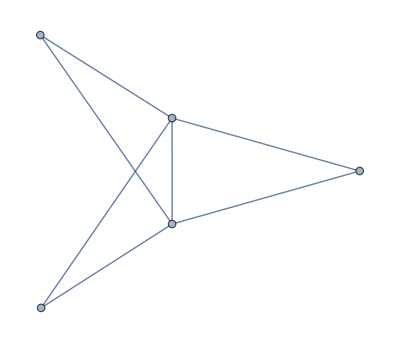
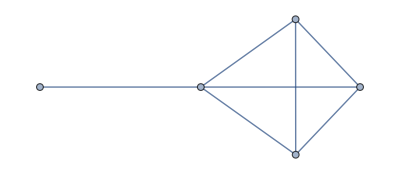
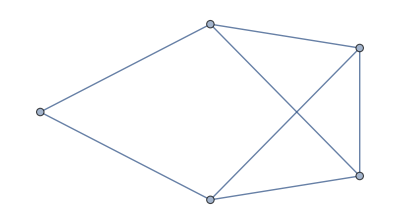
{{-Graphics-,-Graphics-,-Graphics-},7}

```mathematica
graphs=SimpleGraphs@5;
forbidden=GraphF@2;
ExtremalGraphs[graphs,forbidden]
```

```mathematica
IGSubisomorphicQ[forbidden,forbidden]
```

True